```mathematica
(*Parameters*)
m=10^-10; (*kg*)
d=50*10^-9; (*m*)
Δx=10*10^-9; (*m*)
t0 = 0; 
τ= 5*10^-43; 
wp = 3*MachinePrecision; (*n times the machine precision of ~15.9 - Recommend choosing n around 3*)

(*Define Constants*)
G=SetPrecision[6.67430*10^-11,wp]; (*m^3 kg^-1 s^-2*)
hbar=SetPrecision[1.054571817*10^-34,wp]; (*J·s*)
c=SetPrecision[299792458,wp]; (*m/s*)
ε0=SetPrecision[8.8541878128*10^-12,wp]; (*F/m*)
ε=SetPrecision[5.7,wp];
R=SetPrecision[10^-6,wp];
C7=SetPrecision[(23*hbar*c*(R^6))/((4*Pi*ε0)^2*(4*Pi))*((ε-1)/(ε+2))^2,wp];

(*Basis*)
L1={{1},{0}}; 
R1={{0},{1}};
L2={{1},{0}};
R2={{0},{1}};

(*Entropy*)
CPEntropy[t_]:=Module[{φ,ΔφLR,ΔφRL,ketPsi,ρ,ρB},
φ=(C7*t)/(hbar*d^7);
	ΔφLR=(C7*t)/(hbar*(d+Δx)^7)-φ;
	ΔφRL=(C7*t)/(hbar*(d-Δx)^7)-φ;
ketPsi=E^(I*φ)/2*(KroneckerProduct[L1,L2+E^(I*ΔφLR)*R2]+KroneckerProduct[R1,R2+E^(I*ΔφRL)*L2]);
ρ=ketPsi.ConjugateTranspose[ketPsi];
ρB= Map[Tr,Partition[ρ,{2,2}],{2}];
S = -Tr[ρB.MatrixLog[ρB]];
Chop[N[S,wp], 10^-20]
];
CPGEntropy[t_]:=Module[{φ,ΔφLR,ΔφRL,ketPsi,ρ,ρB},
φ=(C7*t)/(hbar*d^7)(1+(G*m^2)/(c^2*d));
	ΔφLR=(C7*t)/(hbar*(d+Δx)^7)(1+(G*m^2)/(c^2*(d+Δx)))-φ;
	ΔφRL=(C7*t)/(hbar*(d-Δx)^7)(1+(G*m^2)/(c^2*(d-Δx)))-φ;
ketPsi=E^(I*φ)/2*(KroneckerProduct[L1,L2+E^(I*ΔφLR)*R2]+KroneckerProduct[R1,R2+E^(I*ΔφRL)*L2]);
ρ=ketPsi.ConjugateTranspose[ketPsi];
ρB= Map[Tr,Partition[ρ,{2,2}],{2}];
S = -Tr[ρB.MatrixLog[ρB]];
Chop[N[S,wp], 10^-20]
];
LogRatio[t_]:= SetPrecision[Log[CPGEntropy[t]/CPEntropy[t]],wp];
```

Entropy with respect to Time

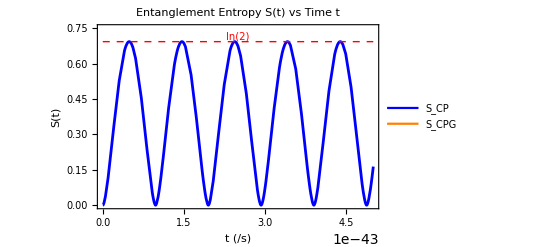

```mathematica
p1=Plot[{Style[CPEntropy[t],Blue],Style[CPGEntropy[t*10^-43],Orange]},{t,t0,τ},Frame->True,FrameLabel->{Style[Row[{"t"," (/s)"}],FontSize->11],Style["S(t)",FontSize->11]},Epilog->{{Red,Dashed,Line[{{0,Log[2]},{τ,Log[2]}}]},Text[Style["ln(2)",Red,Italic,10],{τ/2,Log[2]+0.02}]},PlotRange->{{t0,τ},{0,0.75}},PlotLabel->Style["Entanglement Entropy S(t) vs Time t",FontSize->12],PlotLegends->Placed[LineLegend[{Blue,Orange,Red},{Style[Subscript["S","CP"],FontSize->10],Style[Subscript["S","CPG"],FontSize->10],None},LegendLayout->"Row"],{0.8,0.2}],TicksStyle->Directive[FontSize->9],WorkingPrecision->wp]
```

Ratio of Entropy with respect to Time

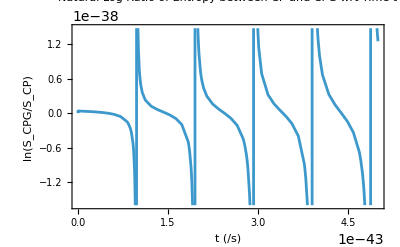

```mathematica
p2=Plot[LogRatio[t],{t,t0,τ},PlotLabel->Style["Natural Log Ratio of Entropy between CP and CPG wrt Time t",FontSize->12],Frame->True,FrameLabel->{Style[Row[{"t"," (/s)"}],FontSize->11],Style[TraditionalForm@Row[{"ln(",Subscript["S","CPG"],"/",Subscript["S","CP"],")"}],FontSize->11]},PlotRange->Automatic,WorkingPrecision->wp,TicksStyle->Directive[FontSize->10]]
```